```mathematica
loadNotebook["uproszczony_off_7_model.nb"];
```

```mathematica
wyrysuj[rozwiazanieu_,tmax_,anim_]:=Module[{},
Plot[Evaluate[{Subscript[θ, u1][t],  Subscript[θ, u2][t]} /.rozwiazanieu], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","skrecenie"}, PlotStyle->{Red, Blue}, PlotLegends->{"θ_u1",  "θ_u2"}] //Print;
Plot[Evaluate[{Subscript[ϕ, u1]'[t],  Subscript[ϕ, u2]'[t]} /.rozwiazanieu], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","predkosc"},PlotStyle->{Red, Blue}, PlotLegends->{"ϕ_u1",  "ϕ_u2"}] //Print;

krzywa1u[t_] = {x[t] ,y[t]} /. rozwiazanieu;

xu[t_] = (x[t]/.rozwiazanieu)[[1]]  ;
yu[t_] = (y[t]/.rozwiazanieu)[[1]]  ;

x1u[t_] = ((x[t]+l*Sin[Subscript[θ, 0][t]]) /. rozwiazanieu  /. {l-> 0.1, R-> 0.03})[[1]];
y1u[t_] = ((y[t]-l*Cos[Subscript[θ, 0][t]]) /. rozwiazanieu  /. {l-> 0.1, R-> 0.03})[[1]];
krzywasu[t_] = ({x1u[t], y1u[t]} /. rozwiazanieu);

x2u[t_] = ((x[t]+2l*Sin[Subscript[θ, 0][t]]) /. rozwiazanieu /. {l-> 0.1, R-> 0.03})[[1]];
y2u[t_] = ((y[t]-2l*Cos[Subscript[θ, 0][t]]) /. rozwiazanieu /. {l-> 0.1, R-> 0.03})[[1]];
krzywa2u[t_] = ({x2u[t], y2u[t]}/. rozwiazanieu);

xpu[t_] = (x1u'[t] /.rozwiazanieu)[[1]];
ypu[t_] = (y1u'[t] /. rozwiazanieu)[[1]];
vu[t_] = Re[Sqrt[(xpu[t])^2+(ypu[t])^2]];

krzywadu[t_]={xd[t],yd[t]};

ParametricPlot[{krzywadu[t],krzywa1u[t], krzywa2u[t], krzywasu[t]},{t,0,1tmax},PlotStyle->{{Black,Thick},Blue,Green,Red}];

curvsu = ParametricPlot[{krzywasu[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Red];
curv1u = ParametricPlot[{krzywa1u[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Blue];
curv2u = ParametricPlot[{krzywa2u[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Yellow];
curvd = ParametricPlot[{xd[t],yd[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Black];
ParametricPlot[{krzywa1u[t],krzywadu[t]},{t, 0, tmax},PlotRange->All,PlotStyle->{Red,Black}, Axes->{True, True}, AxesOrigin->{0,0}] // Print;
p1x[t_]=((x[t]+0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p1y[t_]=((y[t]+0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p2x[t_]=((x[t]-0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p2y[t_]=((y[t]-0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p3x[t_]=((x2u[t]+0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
p3y[t_]=((y2u[t]+0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
p4x[t_]=((x2u[t]-0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
p4y[t_]=((y2u[t]-0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
a2=Animate[
Show[
{curvsu, curv1u, curv2u },
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{x1u[t],y1u[t]}]]}],
Graphics[
{Thickness[0.006],Green,
Line[
{
Dynamic[{xu[t],yu[t]}],
Dynamic[{x2u[t],y2u[t]}]
}
]
}],
Graphics[
{Thickness[0.009],Blue,
Line[
{
Dynamic[{p1x[t],p1y[t]}],
Dynamic[{p2x[t],p2y[t]}]
}
]
}],
Graphics[
{Thickness[0.009],Red,
Line[
{
Dynamic[{p3x[t],p3y[t]}],
Dynamic[{p4x[t],p4y[t]}]
}
]
}]
}
],
{t,0,tmax}];
If[anim,Print[a2],0];
0
];
```

```mathematica
{xd[t_],yd[t_]}=osemka[t,3];
k[t_]=arcCurvature[xd[t],yd[t],t];
xdst=Table[{arcLength[xd[s],yd[s],s,t],xd[t]},{t,0,100,0.01}];
ydst=Table[{arcLength[xd[s],yd[s],s,t],yd[t]},{t,0,100,0.01}];
xds=Interpolation[xdst];
yds=Interpolation[ydst];
Cc=Table[{arcLength[xd[s],yd[s],s,t],k[t]},{t,0,100,0.01}];
t1=Interpolation[Cc];
t2[s_]=D[t1[s],s];
tStart[x0_,y0_]:=(
dist[t_]=Sqrt[(xd[t]-x0)^2+(yd[t]-y0)^2];
t0=t/.Last[FindMinimum[dist[t],{t,0}]];
t0
);

(*ParametricPlot[{xd[t],yd[t]},{t,0,tmax}]
Plot[t1[s],{s,0,12.54},PlotRange->All]
Plot[t2[s],{s,0,12.54},PlotRange->All]*)
```

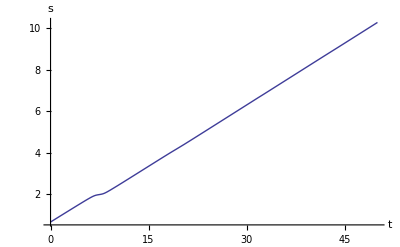

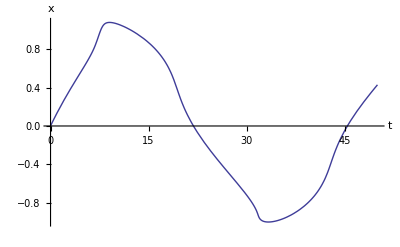

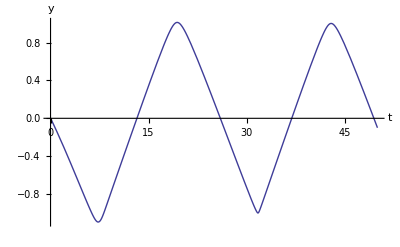

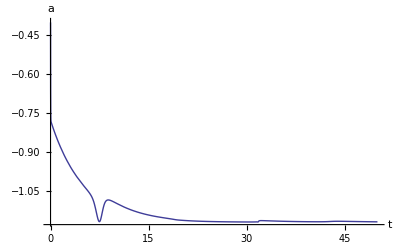

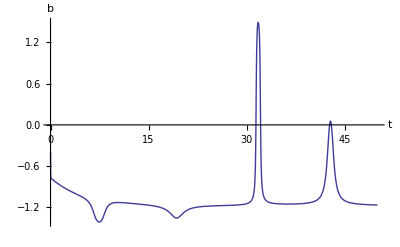

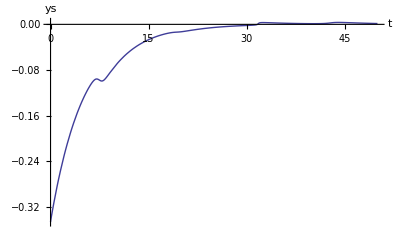

{-0.0999456}

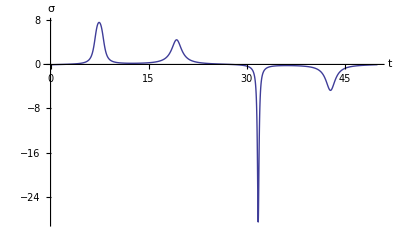

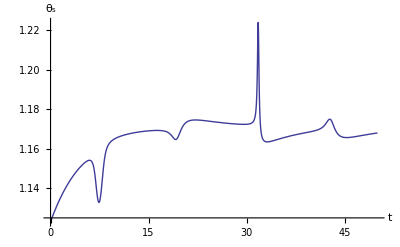

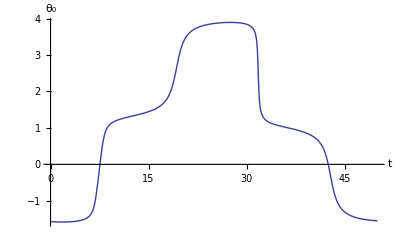

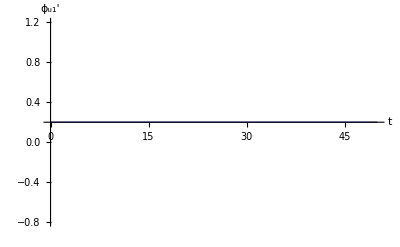

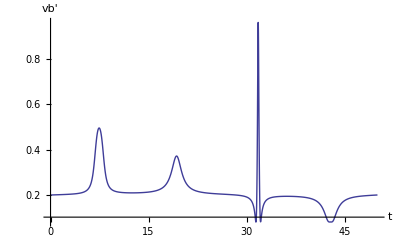

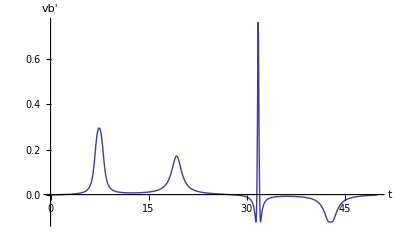

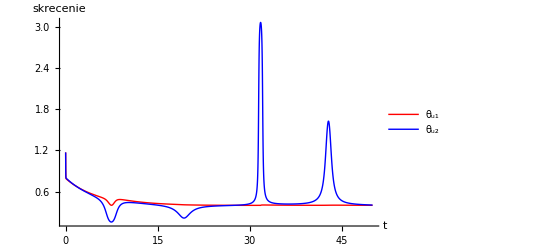

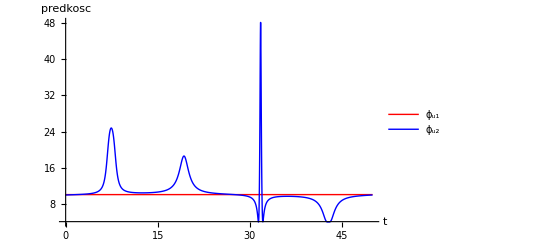

```mathematica
pstrona = Transpose[G2u.Transpose[{ηu[t]}]][[1]];
lstrona = D[qu[t],t];
(*pstrona[[5]]=v*Sqrt[(0.2*σ[t]-Sin[α[t]])^2+(Cos[α[t]])^2]/0.02;
pstrona[[3]]=v*σ[t];*)

lstrona=Join[lstrona,{D[Subscript[β, d][t],t]}];
pstrona=Join[pstrona,{(D[α[t],t](1-2l*σ[t]*Sin[α[t]])-2l*D[σ[t],t]Cos[α[t]])/((2l*σ[t]-Sin[α[t]])^2+Cos[α[t]]^2)}];

Subscript[k, β]=1;
lstrona=Join[lstrona,{D[β[t],t]}];
pstrona=Join[pstrona,{(D[α[t],t](1-2l*σ[t]*Sin[α[t]])-2l*D[σ[t],t]Cos[α[t]])/((2l*σ[t]-Sin[α[t]])^2+Cos[α[t]]^2)-Subscript[k, β](β[t]-Subscript[β, d][t])}];

k1=500;
k2=500;
v=0.2;
cc = t1[Abs[s[t]]];(*t1[s[t]];*)
gc=t1[Abs[s[t]]];(*t2[s[t]];*)
cy=(1/(1-cc*Subscript[y, s][t]));
lstrona=Join[lstrona,{D[s[t],t]}];
pstrona=Join[pstrona,{v*Cos[Subscript[θ, s][t]+α[t]]*cy}];

lstrona=Join[lstrona,{D[Subscript[y, s][t],t]}];
pstrona=Join[pstrona,{v*Sin[Subscript[θ, s][t]+α[t]]}];

lstrona=Join[lstrona,{D[Subscript[θ, s][t],t]}];
pstrona=Join[pstrona,{v*(σ[t]-cc*Cos[Subscript[θ, s][t]+α[t]]*cy)}];

s1=Sin[Subscript[θ, s][t]+α[t]];
c1=Cos[Subscript[θ, s][t]+α[t]];
lstrona=Join[lstrona,{D[α[t],t]}];
pstrona=Join[pstrona,{v*c1*cy*(Subscript[y, s][t]c1*cy*(gc*s1-k1*c1)+s1(cc*s1-k2*c1*Sign[v*c1*cy]+cc))-v*σ[t]}];

Subscript[θ, d]=Pi/2-0.4;
eth=Subscript[θ, s][t]-Subscript[θ, d];
lstrona=Join[lstrona,{D[σ[t],t]}];
pstrona=Join[pstrona,{v*c1*cy(c1*cy(-k1*eth+(gc))+σ[t](Subscript[y, s][t]*c1*cy(gc*c1+k1*s1)+s1*(cc*c1+k2*s1*Sign[v*c1*cy]))-k2*(σ[t]-cc*c1*cy)Sign[v*c1*cy])}];

Subscript[β, 0]=-0.4;
Subscript[α, 0]=-0.4;
θm0=0;
tmax =50;
t00=1;
x0=0;
y0=0;
t0=tStart[x0,y0];
s0=arcLength[xd[s],yd[s],s,t0];
ys0=Sqrt[(xd[t0]-x0)^2+(yd[t0]-y0)^2];
θc0=ArcTan[xd'[t],yd'[t]]/.{t->t0};
q0={x[0]== x0, y[0]==y0, Subscript[θ, 0][0]==θm0-Pi/2, Subscript[θ, u1][0]==Subscript[α, 0]+Pi/2, Subscript[ϕ, u1][0]==0, Subscript[θ, u2][0]== Subscript[β, 0]+Pi/2, Subscript[ϕ, u2][0]==0,s[0]==s0,Subscript[y, s][0]==-ys0,Subscript[θ, s][0]==θm0-θc0,Subscript[β, d][0]==Subscript[β, 0], β[0]==Subscript[β, 0],α[0]==Subscript[α, 0],σ[0]==(1/0.2)*(Sin[Subscript[α, 0]]-Tan[Subscript[β, 0]]Cos[Subscript[α, 0]])};
rownanie = Apply[Equal, Transpose[{lstrona, pstrona}],1];
tosolve = (rownanie /.{Subscript[η, 1][t] ->D[α[t],t], Subscript[η, 2][t]->v/0.02,Subscript[η, 3][t]->D[β[t],t],l-> 0.1, Subscript[r, 1]->0.02, Subscript[r, 2]->0.02}) ~Join~  q0;
roz = NDSolve[tosolve, {x,y,s, Subscript[θ, 0],Subscript[θ, u1], Subscript[ϕ, u1],Subscript[θ, u2], Subscript[ϕ, u2],Subscript[y, s],Subscript[θ, s],β,α,σ,Subscript[β, d]}, {t,0,tmax}, Method->Automatic, MaxSteps->1000000];
Plot[s[t]/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","s"}]
Plot[x[t]/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","x"}]
Plot[y[t]/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","y"}]
Plot[α[t]/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","a"}]
Plot[β[t]/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","b"}]
Plot[Subscript[y, s][t]/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","ys"}]
y[tmax]/.roz
Plot[σ[t]/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","σ"}]
Plot[Subscript[θ, s][t]/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","θ_s"}]
Plot[Subscript[θ, 0][t]/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","θ_0"}]
Plot[Subscript[ϕ, u1]'[t]*0.02/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","ϕ_u1'"}]
Plot[(v*Sqrt[(0.2*σ[t]-Sin[α[t]])^2+(Cos[α[t]])^2])/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","vb'"}]
Plot[(v*Sqrt[(0.2*σ[t]-Sin[α[t]])^2+(Cos[α[t]])^2] - Subscript[ϕ, u1]'[t]*0.02)/.roz,{t,0,tmax}, PlotRange->All,AxesLabel->{"t","vb'"}]
wyrysuj[roz,tmax,True];
```

```mathematica
Pi/2-1// N
```

0.570796